```mathematica
ClearAll;
```

```mathematica
f = Piecewise[{{1,0≤t<1}}]
```

Piecewise[{{1, 0≤t<1}, {0, True}}]

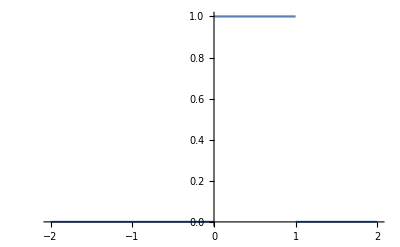

```mathematica
Plot[f,{t,-2,2}]
```

```mathematica
s = FourierTransform[f,t,w]
```

(ⅈ-ⅈ Cos[w]+Sin[w])/(√(2 π) w)

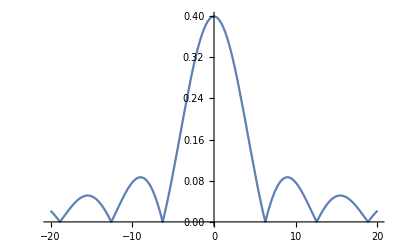

```mathematica
Plot[Abs[s],{w,-20,20}]
```

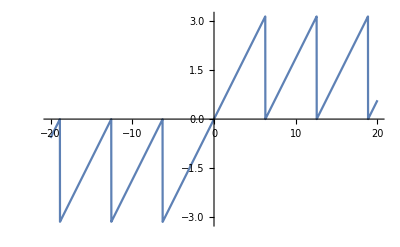

```mathematica
Plot[Arg[s],{w,-20,20}]
```

```mathematica
FourierTransform[Sin[2Pi*t],t,w]
```

ⅈ √(π/2) DiracDelta[-2 π+w]-ⅈ √(π/2) DiracDelta[2 π+w]

ⅈ √(π/2) DiracDelta[-2 π+w]-ⅈ √(π/2) DiracDelta[2 π+w]

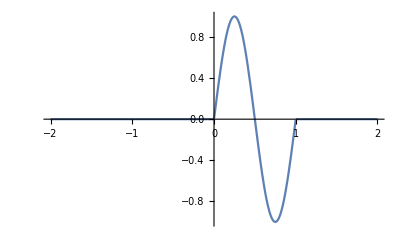

```mathematica
ⅈ √(π/2) DiracDelta[-2 π+w]-ⅈ √(π/2) DiracDelta[2 π+w]
Plot[f*Sin[2Pi*t],{t,-2,2}]
```

```mathematica
FourierTransform[f*Sin[2Pi*t],t,w]
```

-(√(2 π) (-1+Cos[w]+ⅈ Sin[w]))/(4 π^2-w^2)

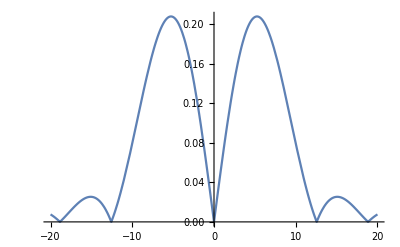

```mathematica
Plot[Abs[%],{w,-20,20}]
```

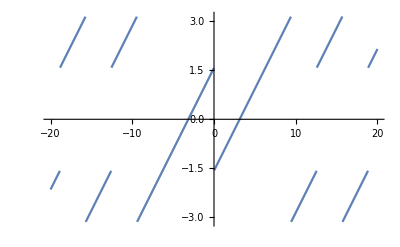

```mathematica
Plot[Arg[%%],{w,-20,20}]
```